```mathematica
u090494e　荒井直幸　2014年11月18日
```

```mathematica
課題１
```

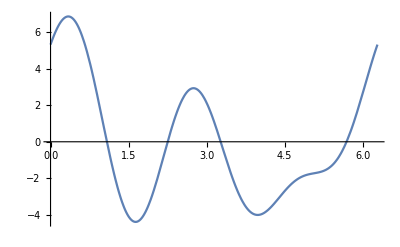

1.21

2.1

0.

3.21

2.31

0.

```mathematica
f1[x_]=2.1 Cos[x]+1.21 Sin[x]+3.21 Cos[2 x]+2.31 Sin[3 x];
Plot[f1[x],{x,0,2 Pi}]
Integrate[f1[x] Sin[x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Cos[x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Sin[2 x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Cos[2 x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Sin[3 x]/Pi,{x,0,2 Pi}]
Integrate[f1[x] Cos[3 x]/Pi,{x,0,2 Pi}]
```

```mathematica
課題２
```

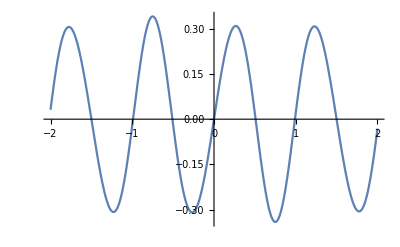

```mathematica
FTS=FourierTrigSeries[x-Round[x],x,10];
Four1=Plot[FTS,{x,-2,2}];
Show[Four1]
```

```mathematica
課題３
```

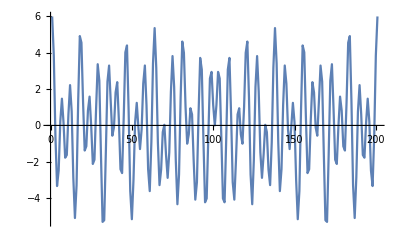

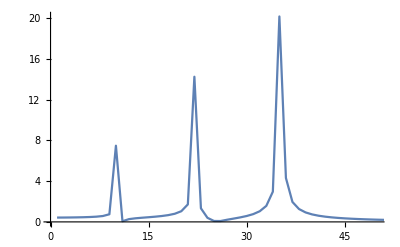

```mathematica
func1[x_]:=Cos[2 Pi o x/200];
o=10;
func2[x_]:=Cos[2 Pi p x/200];
p=22;
func3[x_]:=Cos[2 Pi q x/200];
q=35;
data1=Table[func1[x]+2 func2[x]+3 func3[x],{x,0,200}];
ListLinePlot[data1]
data2=Abs[Fourier[data1]];
data3=Rest[data2];
graph1=ListLinePlot[data3,PlotRange->{{0,50},All}]
```

```mathematica
課題４
```

```mathematica
AM波は
```

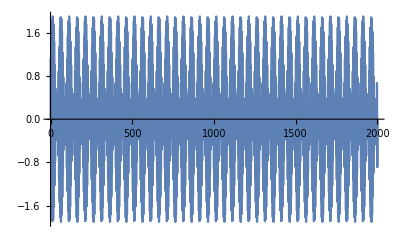

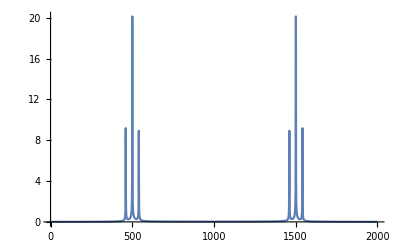

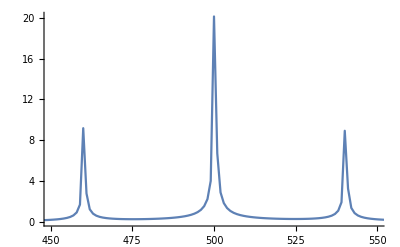

```mathematica
func4[x_]:=(1.0+0.9 Sin[2 Pi 40 x/2000]) Sin[2 Pi 500 x/2000];
data4=Table[func4[x],{x,0,2000}];
ListLinePlot[data4]
data5=Abs[Fourier[data4]];
data6=Rest[data5];
graph2=ListLinePlot[data6,PlotRange->{{0,2000},All}]
graph3=ListLinePlot[data6,PlotRange->{{450,550},All}]
```

```mathematica
FM波は
```

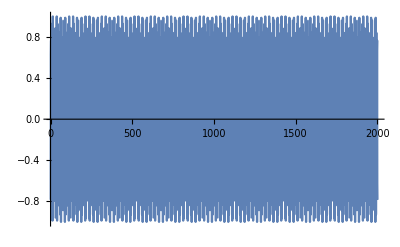

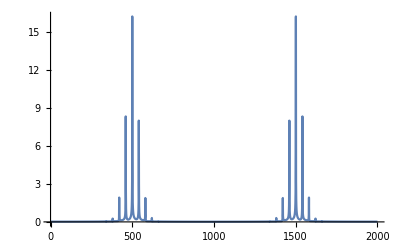

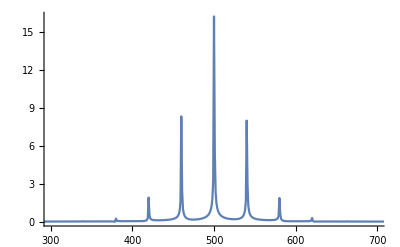

```mathematica
func5[x_]:=Sin[2 Pi 500 x/2000-0.9 Cos[2 Pi 40 x/2000]];
data7=Table[func5[x],{x,0,2000}];
ListLinePlot[data7]
data8=Abs[Fourier[data7]];
data9=Rest[data8];
graph4=ListLinePlot[data9,PlotRange->{{0,2000},All}]
graph5=ListLinePlot[data9,PlotRange->{{300,700},All}]
```

```mathematica
AM波のほうが占有する周波数幅が狭い
```